# Problem 0

```mathematica
SetDirectory["/home/ethan/spring20/comphys/week4/coding"];
SetOptions[ListPlot, Frame -> True, BaseStyle -> {FontFamily -> "Helvitica", FontSize -> 20, FontColor->Black}, LabelStyle-> {GrayLevel[0]}, ImageSize -> Full];
```

```mathematica
(* Name   dt         T      m0    x0    y0   vx0   vy0   m1      x1    y1    vx1   vy1       m2          x2      y2    vx2   vy2*)
data = Partition[ReadList[  "!./nbody 0.001     1     1     0      0    0   0 0.0000001     1     0     0     6.283185     0.001     0     0     0     0", Number], 13];
ListPlot[{data[[All, {4,5} ]], data[[All, {6,7}]], data[[All, {2,3}]]}, PlotRange->All, FrameLabel-> {"X Position (AU)", "Y Position (AU)"}, PlotLabel->"Earth-like Object", PlotLegends->{"Earth"}, Joined->True ]//Rasterize
```

-Graphics-

# Problem 1

## Part 1

-Graphics-

-Graphics-

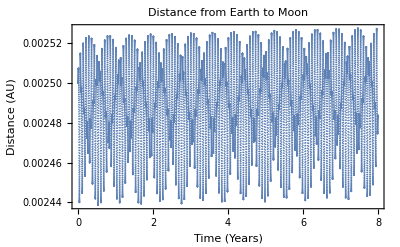

-Graphics-

-Graphics-

-Graphics-

«2 more identical outputs»

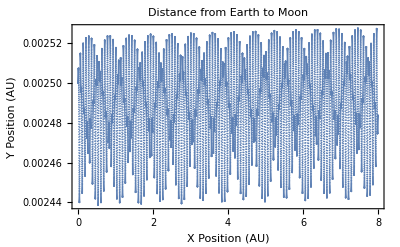

-Graphics-

-Graphics-

-Graphics-

```mathematica
dt = 0.0003;
time = 8;
m0 = 1;
x0 = 0;
y0 = 0;
vx0= 0;
vy0 = 0;
m1 = N[3*10^-6, 20];
x1 = 1;
y1 = 0;
vx1 = 0;
vy1 = N[2*Pi, 20];
m2 = N[3.7*10^-8,20];
x2 = 1.0025;
y2 = 0;
vx2 = 0;
vy2 = N[2.*Pi+ Sqrt[4.*Pi*Pi*(m1+m2)/0.0025],20];
data = 
Partition[
ReadList[ "!./nbody "<>
ToString[NumberForm[dt, ScientificNotationThreshold->{-20,20}]] <>" "<>ToString[NumberForm[time, ScientificNotationThreshold->{-20,20}]] <>" "<>ToString[NumberForm[m0, ScientificNotationThreshold->{-20,20}]] <>" "<>ToString[NumberForm[x0, ScientificNotationThreshold->{-20,20}]] <>" "<>ToString[NumberForm[y0, ScientificNotationThreshold->{-20,20}]] <>" "<>ToString[NumberForm[vx0, ScientificNotationThreshold->{-20,20}]] <>" "<>ToString[NumberForm[vy0, ScientificNotationThreshold->{-20,20}]] <>" "<>ToString[NumberForm[m1, ScientificNotationThreshold->{-20,20}]] <>" "<>ToString[NumberForm[x1, ScientificNotationThreshold->{-20,20}]] <>" "<>ToString[NumberForm[y1, ScientificNotationThreshold->{-20,20}]] <>" "<>ToString[NumberForm[vx1, ScientificNotationThreshold->{-20,20}]] <>" "<>ToString[NumberForm[vy1, ScientificNotationThreshold->{-20,20}]] <>" "<>ToString[NumberForm[m2, ScientificNotationThreshold->{-20,20}]] <>" "<>ToString[NumberForm[x2, ScientificNotationThreshold->{-20,20}]] <>" "<>ToString[NumberForm[y2, ScientificNotationThreshold->{-20,20}]] <>" "<>ToString[NumberForm[vx2, ScientificNotationThreshold->{-20,20}]] <>" "<>ToString[NumberForm[vy2, ScientificNotationThreshold->{-20,20}]] , Number], 13];
ListPlot[{data[[All, {2,3}]], data[[All, {4,5}]], data[[All,{6,7}]]},PlotLabel->"Earths Orbit in One Year", FrameLabel->{"Y Coordinate (AU)", "X Coordinate (AU)"},PlotLegends->{"Sun","Earth", "Moon"}, Joined->True ]//Rasterize
ListPlot[ data[[All, {6,7}]]-data[[All,{4,5}]], PlotRange->Full,PlotLabel-> " Moon's Relative Position to Earth", FrameLabel-> {"X Position (AU)", "Y Position (AU)"},PlotLegends->{"Moon"}, Joined->True ]//Rasterize
ListPlot[Thread[{Flatten[data[[All, {1}]]],Table[EuclideanDistance[data[[i, {6,7}]],data[[i,{4,5}]]], {i,Length[data]}]}], FrameLabel-> {"Time (Years)", "Distance (AU)"}, PlotLabel-> "Distance from Earth to Moon"]
G = 4*Pi*Pi;
KE = 0.5m0 * (data[[All, 8]]^2+data[[All, 9]]^2)+
0.5m1     * (data[[All, 10]]^2+data[[All, 11]]^2)+
0.5m2     * (data[[All, 12]]^2+data[[All, 13]]^2);
PE = N[(-G*m0*m1)/((data[[All, 2]]-data[[All, 4]])^2+(data[[All, 3]]-data[[All,5  ]])^2)^0.5+    (-G*m0*m2)/         ((data[[All, 2]]-data[[All, 6]])^2+(data[[All, 3]]-data[[All,7  ]])^2)^0.5+(-G*m1*m2)/         ((data[[All, 4]]-data[[All, 6]])^2+(data[[All, 5]]-data[[All,7  ]])^2)^0.5,20];
TE = KE + PE;
ListPlot[Thread[{data[[All, 1]],KE}],PlotLabel->"Kinetic Energy of Sun, Earth, Moon System", FrameLabel->{"Time (Years}", "Energy (Sol*AU^2*Year^-2)"}, PlotLegends->{"KE"}, Joined->True ]//Rasterize
ListPlot[Thread[{data[[All, 1]],PE}],PlotLabel->"Potential Energy of Sun, Earth, Moon System", FrameLabel->{"Time (Years}", "Energy (Sol*AU^2*Year^-2)"},PlotLegends->{"PE"}, Joined->True ]//Rasterize
ListPlot[Thread[{data[[All, 1]],TE}],PlotLabel->"Total Energy of Sun, Earth, Moon System", FrameLabel->{"Time (Years}", "Energy (Sol*AU^2*Year^-2)"},PlotLegends->{"TE"}, Joined->True ]//Rasterize
```

## Part 2

-Graphics-

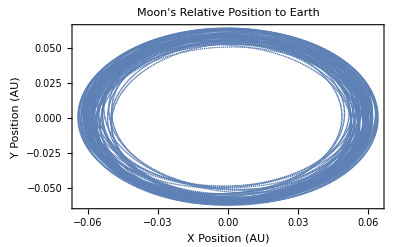

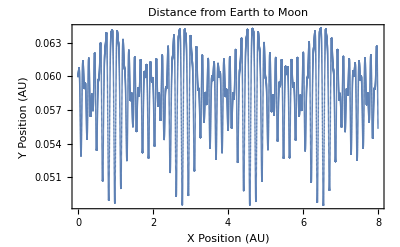

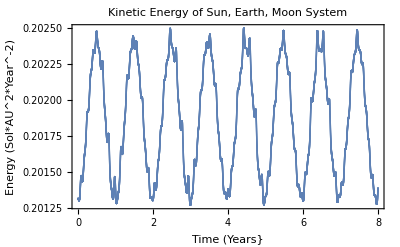

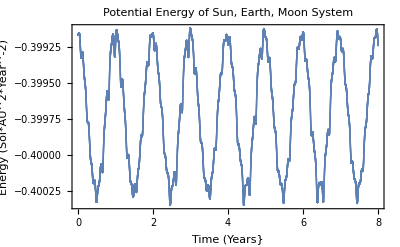

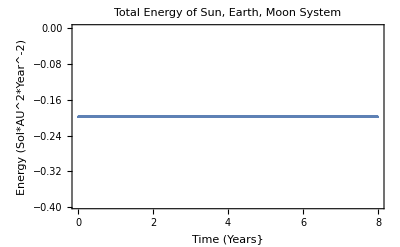

```mathematica
dt = 0.0003;
time = 8;
m0 = 1;
x0 = 0;
y0 = 0;
vx0= 0;
vy0 = 0;
m1 = N[10^-2, 20];
x1 = 1;
y1 = 0;
vx1 = 0;
vy1 = N[2*Pi, 20];
m2 = N[10^-4,20];
x2 = 1.06;
y2 = 0;
vx2 = 0;
vy2 = N[2.*Pi+ Sqrt[4.*Pi*Pi*(m1+m2)/(x2-x1)],20];
data = 
Partition[
ReadList[ "!./nbody "<>
ToString[NumberForm[dt, ScientificNotationThreshold->{-20,20}]] <>" "<>ToString[NumberForm[time, ScientificNotationThreshold->{-20,20}]] <>" "<>ToString[NumberForm[m0, ScientificNotationThreshold->{-20,20}]] <>" "<>ToString[NumberForm[x0, ScientificNotationThreshold->{-20,20}]] <>" "<>ToString[NumberForm[y0, ScientificNotationThreshold->{-20,20}]] <>" "<>ToString[NumberForm[vx0, ScientificNotationThreshold->{-20,20}]] <>" "<>ToString[NumberForm[vy0, ScientificNotationThreshold->{-20,20}]] <>" "<>ToString[NumberForm[m1, ScientificNotationThreshold->{-20,20}]] <>" "<>ToString[NumberForm[x1, ScientificNotationThreshold->{-20,20}]] <>" "<>ToString[NumberForm[y1, ScientificNotationThreshold->{-20,20}]] <>" "<>ToString[NumberForm[vx1, ScientificNotationThreshold->{-20,20}]] <>" "<>ToString[NumberForm[vy1, ScientificNotationThreshold->{-20,20}]] <>" "<>ToString[NumberForm[m2, ScientificNotationThreshold->{-20,20}]] <>" "<>ToString[NumberForm[x2, ScientificNotationThreshold->{-20,20}]] <>" "<>ToString[NumberForm[y2, ScientificNotationThreshold->{-20,20}]] <>" "<>ToString[NumberForm[vx2, ScientificNotationThreshold->{-20,20}]] <>" "<>ToString[NumberForm[vy2, ScientificNotationThreshold->{-20,20}]] , Number], 13];
ListPlot[{data[[All, {2,3}]], data[[All, {4,5}]], data[[All,{6,7}]]},PlotLabel->"Earths Orbit for 8 Years", FrameLabel->{"Y Coordinate (AU)", "X Coordinate (AU)"},PlotLegends->{"Sun","Earth", "Moon"}, Joined->True ]//Rasterize
ListPlot[ data[[All, {6,7}]]-data[[All,{4,5}]], PlotRange->Full,PlotLabel-> " Moon's Relative Position to Earth", FrameLabel-> {"X Position (AU)", "Y Position (AU)"}]
ListPlot[Thread[{Flatten[data[[All, {1}]]],Table[EuclideanDistance[data[[i, {6,7}]],data[[i,{4,5}]]], {i,Length[data]}]}], FrameLabel-> {"X Position (AU)", "Y Position (AU)"}, PlotLabel-> "Distance from Earth to Moon"]
G = 4*Pi*Pi;
KE = 0.5m0 * (data[[All, 8]]^2+data[[All, 9]]^2)+
0.5m1     * (data[[All, 10]]^2+data[[All, 11]]^2)+
0.5m2     * (data[[All, 12]]^2+data[[All, 13]]^2);
PE = N[(-G*m0*m1)/((data[[All, 2]]-data[[All, 4]])^2+(data[[All, 3]]-data[[All,5  ]])^2)^0.5+    (-G*m0*m2)/         ((data[[All, 2]]-data[[All, 6]])^2+(data[[All, 3]]-data[[All,7  ]])^2)^0.5+(-G*m1*m2)/         ((data[[All, 4]]-data[[All, 6]])^2+(data[[All, 5]]-data[[All,7  ]])^2)^0.5,20];
TE = KE + PE;
ListPlot[Thread[{data[[All, 1]],KE}],PlotLabel->"Kinetic Energy of Sun, Earth, Moon System", FrameLabel->{"Time (Years}", "Energy (Sol*AU^2*Year^-2)"}]
ListPlot[Thread[{data[[All, 1]],PE}],PlotLabel->"Potential Energy of Sun, Earth, Moon System", FrameLabel->{"Time (Years}", "Energy (Sol*AU^2*Year^-2)"}]
ListPlot[Thread[{data[[All, 1]],TE}],PlotLabel->"Total Energy of Sun, Earth, Moon System", FrameLabel->{"Time (Years}", "Energy (Sol*AU^2*Year^-2)"}]
```

## Part 3

-Graphics-

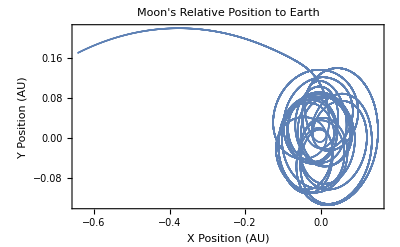

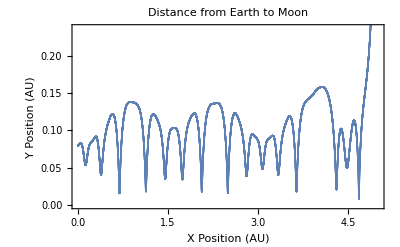

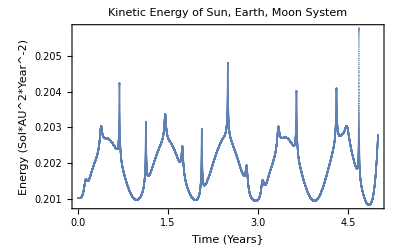

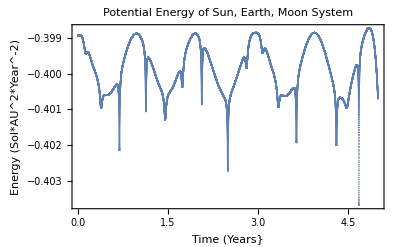

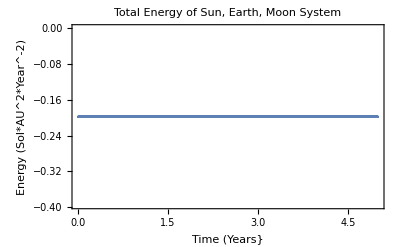

```mathematica
dt = 0.0001;
time = 5;
m0 = 1;
x0 = 0;
y0 = 0;
vx0= 0;
vy0 = 0;
m1 = N[10^-2, 20];
x1 = 1;
y1 = 0;
vx1 = 0;
vy1 = N[2*Pi, 20];
m2 = N[10^-4,20];
x2 = 1.08;
y2 = 0;
vx2 = 0;
vy2 = N[2.*Pi+ Sqrt[4.*Pi*Pi*(m1+m2)/(x2-x1)],20];
data = 
Partition[
ReadList[ "!./nbody "<>
ToString[NumberForm[dt, ScientificNotationThreshold->{-20,20}]] <>" "<>ToString[NumberForm[time, ScientificNotationThreshold->{-20,20}]] <>" "<>ToString[NumberForm[m0, ScientificNotationThreshold->{-20,20}]] <>" "<>ToString[NumberForm[x0, ScientificNotationThreshold->{-20,20}]] <>" "<>ToString[NumberForm[y0, ScientificNotationThreshold->{-20,20}]] <>" "<>ToString[NumberForm[vx0, ScientificNotationThreshold->{-20,20}]] <>" "<>ToString[NumberForm[vy0, ScientificNotationThreshold->{-20,20}]] <>" "<>ToString[NumberForm[m1, ScientificNotationThreshold->{-20,20}]] <>" "<>ToString[NumberForm[x1, ScientificNotationThreshold->{-20,20}]] <>" "<>ToString[NumberForm[y1, ScientificNotationThreshold->{-20,20}]] <>" "<>ToString[NumberForm[vx1, ScientificNotationThreshold->{-20,20}]] <>" "<>ToString[NumberForm[vy1, ScientificNotationThreshold->{-20,20}]] <>" "<>ToString[NumberForm[m2, ScientificNotationThreshold->{-20,20}]] <>" "<>ToString[NumberForm[x2, ScientificNotationThreshold->{-20,20}]] <>" "<>ToString[NumberForm[y2, ScientificNotationThreshold->{-20,20}]] <>" "<>ToString[NumberForm[vx2, ScientificNotationThreshold->{-20,20}]] <>" "<>ToString[NumberForm[vy2, ScientificNotationThreshold->{-20,20}]] , Number], 13];
ListPlot[{data[[All, {2,3}]], data[[All, {4,5}]], data[[All,{6,7}]]},PlotLabel->"Alternate Earth Orbit for 8 Years", FrameLabel->{"Y Coordinate (AU)", "X Coordinate (AU)"},PlotLegends->{"Sun","Earth", "Moon"}, Joined->True ]//Rasterize
ListPlot[ data[[All, {6,7}]]-data[[All,{4,5}]], PlotRange->Full,PlotLabel-> " Moon's Relative Position to Earth", FrameLabel-> {"X Position (AU)", "Y Position (AU)"}]
ListPlot[Thread[{Flatten[data[[All, {1}]]],Table[EuclideanDistance[data[[i, {6,7}]],data[[i,{4,5}]]], {i,Length[data]}]}], FrameLabel-> {"X Position (AU)", "Y Position (AU)"}, PlotLabel-> "Distance from Earth to Moon"]
G = 4*Pi*Pi;
KE = 0.5m0 * (data[[All, 8]]^2+data[[All, 9]]^2)+
0.5m1     * (data[[All, 10]]^2+data[[All, 11]]^2)+
0.5m2     * (data[[All, 12]]^2+data[[All, 13]]^2);
PE = N[(-G*m0*m1)/((data[[All, 2]]-data[[All, 4]])^2+(data[[All, 3]]-data[[All,5  ]])^2)^0.5+    (-G*m0*m2)/         ((data[[All, 2]]-data[[All, 6]])^2+(data[[All, 3]]-data[[All,7  ]])^2)^0.5+(-G*m1*m2)/         ((data[[All, 4]]-data[[All, 6]])^2+(data[[All, 5]]-data[[All,7  ]])^2)^0.5,20];
TE = KE + PE;
ListPlot[Thread[{data[[All, 1]],KE}],PlotLabel->"Kinetic Energy of Sun, Earth, Moon System", FrameLabel->{"Time (Years}", "Energy (Sol*AU^2*Year^-2)"}]
ListPlot[Thread[{data[[All, 1]],PE}],PlotLabel->"Potential Energy of Sun, Earth, Moon System", FrameLabel->{"Time (Years}", "Energy (Sol*AU^2*Year^-2)"}]
ListPlot[Thread[{data[[All, 1]],TE}],PlotLabel->"Total Energy of Sun, Earth, Moon System", FrameLabel->{"Time (Years}", "Energy (Sol*AU^2*Year^-2)"}]
```

## Part 4

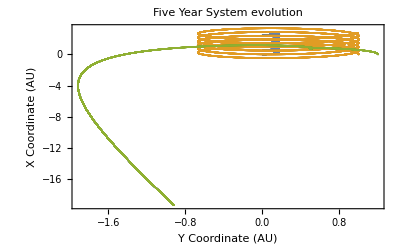

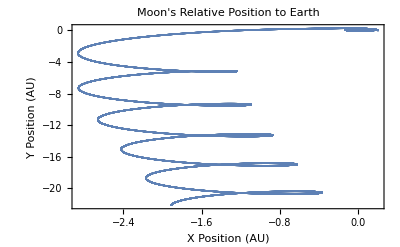

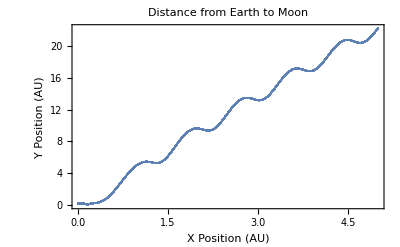

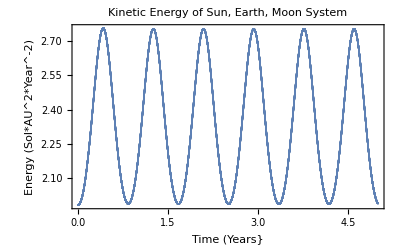

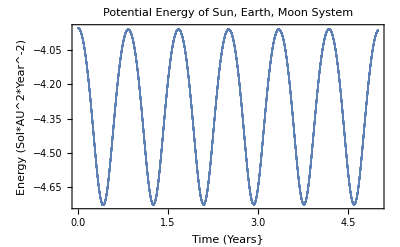

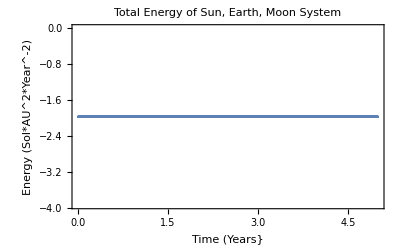

```mathematica
dt = 0.0001;
time = 5;
m0 = 1;
x0 = 0;
y0 = 0;
vx0= 0;
vy0 = 0;
m1 = N[10^-1, 20];
x1 = 1;
y1 = 0;
vx1 = 0;
vy1 = N[2*Pi, 20];
m2 = N[10^-4,20];
x2 = 1.2;
y2 = 0;
vx2 = 0;
vy2 = N[2.*Pi+ Sqrt[4.*Pi*Pi*(m1+m2)/(x2-x1)],20];
data = 
Partition[
ReadList[ "!./nbody "<>
ToString[NumberForm[dt, ScientificNotationThreshold->{-20,20}]] <>" "<>ToString[NumberForm[time, ScientificNotationThreshold->{-20,20}]] <>" "<>ToString[NumberForm[m0, ScientificNotationThreshold->{-20,20}]] <>" "<>ToString[NumberForm[x0, ScientificNotationThreshold->{-20,20}]] <>" "<>ToString[NumberForm[y0, ScientificNotationThreshold->{-20,20}]] <>" "<>ToString[NumberForm[vx0, ScientificNotationThreshold->{-20,20}]] <>" "<>ToString[NumberForm[vy0, ScientificNotationThreshold->{-20,20}]] <>" "<>ToString[NumberForm[m1, ScientificNotationThreshold->{-20,20}]] <>" "<>ToString[NumberForm[x1, ScientificNotationThreshold->{-20,20}]] <>" "<>ToString[NumberForm[y1, ScientificNotationThreshold->{-20,20}]] <>" "<>ToString[NumberForm[vx1, ScientificNotationThreshold->{-20,20}]] <>" "<>ToString[NumberForm[vy1, ScientificNotationThreshold->{-20,20}]] <>" "<>ToString[NumberForm[m2, ScientificNotationThreshold->{-20,20}]] <>" "<>ToString[NumberForm[x2, ScientificNotationThreshold->{-20,20}]] <>" "<>ToString[NumberForm[y2, ScientificNotationThreshold->{-20,20}]] <>" "<>ToString[NumberForm[vx2, ScientificNotationThreshold->{-20,20}]] <>" "<>ToString[NumberForm[vy2, ScientificNotationThreshold->{-20,20}]] , Number], 13];
ListPlot[{data[[All, {2,3}]], data[[All, {4,5}]], data[[All,{6,7}]]},PlotLabel->"Five Year System evolution", FrameLabel->{"Y Coordinate (AU)", "X Coordinate (AU)"}]
ListPlot[ data[[All, {6,7}]]-data[[All,{4,5}]], PlotRange->Full,PlotLabel-> "Moon's Relative Position to Earth", FrameLabel-> {"X Position (AU)", "Y Position (AU)"}]
ListPlot[Thread[{Flatten[data[[All, {1}]]],Table[EuclideanDistance[data[[i, {6,7}]],data[[i,{4,5}]]], {i,Length[data]}]}], FrameLabel-> {"X Position (AU)", "Y Position (AU)"}, PlotLabel-> "Distance from Earth to Moon"]
G = 4*Pi*Pi;
KE = 0.5m0 * (data[[All, 8]]^2+data[[All, 9]]^2)+
0.5m1     * (data[[All, 10]]^2+data[[All, 11]]^2)+
0.5m2     * (data[[All, 12]]^2+data[[All, 13]]^2);
PE = N[(-G*m0*m1)/((data[[All, 2]]-data[[All, 4]])^2+(data[[All, 3]]-data[[All,5  ]])^2)^0.5+    (-G*m0*m2)/         ((data[[All, 2]]-data[[All, 6]])^2+(data[[All, 3]]-data[[All,7  ]])^2)^0.5+(-G*m1*m2)/         ((data[[All, 4]]-data[[All, 6]])^2+(data[[All, 5]]-data[[All,7  ]])^2)^0.5,20];
TE = KE + PE;
ListPlot[Thread[{data[[All, 1]],KE}],PlotLabel->"Kinetic Energy of Sun, Earth, Moon System", FrameLabel->{"Time (Years}", "Energy (Sol*AU^2*Year^-2)"}]
ListPlot[Thread[{data[[All, 1]],PE}],PlotLabel->"Potential Energy of Sun, Earth, Moon System", FrameLabel->{"Time (Years}", "Energy (Sol*AU^2*Year^-2)"}]
ListPlot[Thread[{data[[All, 1]],TE}],PlotLabel->"Total Energy of Sun, Earth, Moon System", FrameLabel->{"Time (Years}", "Energy (Sol*AU^2*Year^-2)"}]
```

# Problem 2

## Part 1

```mathematica
dt = 0.00003;
time = 5;
m0 = 1;
x0 = 0;
y0 = 0;
vx0= 1;
vy0 = -1;
m1 = 1;
x1 = 1;
y1 = 0;
vx1 = 0;
vy1 = 6;
m2 =  1;
x2 = 2;
y2 = 0;
vx2 = 0;
vy2 = -6;
data = 
Partition[
ReadList[ "!./nbody "<>
ToString[NumberForm[dt, ScientificNotationThreshold->{-20,20}]] <>" "<>ToString[NumberForm[time, ScientificNotationThreshold->{-20,20}]] <>" "<>ToString[NumberForm[m0, ScientificNotationThreshold->{-20,20}]] <>" "<>ToString[NumberForm[x0, ScientificNotationThreshold->{-20,20}]] <>" "<>ToString[NumberForm[y0, ScientificNotationThreshold->{-20,20}]] <>" "<>ToString[NumberForm[vx0, ScientificNotationThreshold->{-20,20}]] <>" "<>ToString[NumberForm[vy0, ScientificNotationThreshold->{-20,20}]] <>" "<>ToString[NumberForm[m1, ScientificNotationThreshold->{-20,20}]] <>" "<>ToString[NumberForm[x1, ScientificNotationThreshold->{-20,20}]] <>" "<>ToString[NumberForm[y1, ScientificNotationThreshold->{-20,20}]] <>" "<>ToString[NumberForm[vx1, ScientificNotationThreshold->{-20,20}]] <>" "<>ToString[NumberForm[vy1, ScientificNotationThreshold->{-20,20}]] <>" "<>ToString[NumberForm[m2, ScientificNotationThreshold->{-20,20}]] <>" "<>ToString[NumberForm[x2, ScientificNotationThreshold->{-20,20}]] <>" "<>ToString[NumberForm[y2, ScientificNotationThreshold->{-20,20}]] <>" "<>ToString[NumberForm[vx2, ScientificNotationThreshold->{-20,20}]] <>" "<>ToString[NumberForm[vy2, ScientificNotationThreshold->{-20,20}]] , Number], 13];
comx = (data[[All, 2]]*m0+data[[All,4]]*m1+data[[All, 6]]*m2)/(m0+m1+m2);
comy = (data[[All, 3]]*m0+data[[All,5]]*m1+data[[All, 7]]*m2)/(m0+m1+m2);
com = Thread[{comx,comy}];
i=10;
{data[[i, {2,3}]] - com[[i]],
data[[i, {4,5}]] - com[[i]],
data[[i, {6,7}]] - com[[i]]};
(*ListAnimate[Table[ListPlot[{{data[[i, {2,3}]] - com[[i]]},
{data[[i, {4,5}]] - com[[i]]},
{data[[i, {6,7}]] - com[[i]]}}, PlotRange-> {{-2,2},{-2,2}}, FrameLabel->{"ΔX From CoM(AU)","ΔY CoM(AU)"}],{i,1, Length[data], 100}],30]*)
ListPlot[{data[[All, {2,3}]] - com, data[[All, {4,5}]] -com, data[[All, {6,7}]]-com},PlotLabel->"3 Body Motion Relative to System Center of Mass"]
ListPlot[{data[[All, {2,3}]], data[[All, {4,5}]], data[[All,{6,7}]]},PlotLabel->"Five Year System Evolution", FrameLabel->{"Y Coordinate (AU)", "X Coordinate (AU)"},PlotLegends->{"Sun","Earth", "Moon"}, Joined->True ]//Rasterize
ListPlot[ data[[All, {6,7}]]-data[[All,{4,5}]], PlotRange->Full,PlotLabel-> " Moon's Relative Position to Earth", FrameLabel-> {"X Position (AU)", "Y Position (AU)"}]
ListPlot[Thread[{Flatten[data[[All, {1}]]],Table[EuclideanDistance[data[[i, {6,7}]],data[[i,{4,5}]]], {i,Length[data]}]}], FrameLabel-> {"X Position (AU)", "Y Position (AU)"}, PlotLabel-> "Distance from Earth to Moon"]
G = 4*Pi*Pi;
KE = 0.5m0 * (data[[All, 8]]^2+data[[All, 9]]^2)+
0.5m1     * (data[[All, 10]]^2+data[[All, 11]]^2)+
0.5m2     * (data[[All, 12]]^2+data[[All, 13]]^2);
PE = N[(-G*m0*m1)/((data[[All, 2]]-data[[All, 4]])^2+(data[[All, 3]]-data[[All,5  ]])^2)^0.5+    (-G*m0*m2)/         ((data[[All, 2]]-data[[All, 6]])^2+(data[[All, 3]]-data[[All,7  ]])^2)^0.5+(-G*m1*m2)/         ((data[[All, 4]]-data[[All, 6]])^2+(data[[All, 5]]-data[[All,7  ]])^2)^0.5,20];
TE = KE + PE;
ListPlot[Thread[{data[[All, 1]],KE}],PlotLabel->"Kinetic Energy of Sun, Earth, Moon System", FrameLabel->{"Time (Years}", "Energy (Sol*AU^2*Year^-2)"}]
ListPlot[Thread[{data[[All, 1]],PE}],PlotLabel->"Potential Energy of Sun, Earth, Moon System", FrameLabel->{"Time (Years}", "Energy (Sol*AU^2*Year^-2)"}]
ListPlot[Thread[{data[[All, 1]],TE}],PlotLabel->"Total Energy of Sun, Earth, Moon System", FrameLabel->{"Time (Years}", "Energy (Sol*AU^2*Year^-2)"}]
```

-Graphics-

-Graphics-

-Graphics-

«4 more identical outputs»

## Part 2

```mathematica
dt = 0.00003;
time = 10;
m0 = 1;
x0 = 0;
y0 = 0;
vx0= 1;
vy0 = -1;
m1 = 1;
x1 = 1;
y1 = 0;
vx1 = 0;
vy1 = 6;
m2 =  1;
x2 = 2;
y2 = 0;
vx2 = 0;
vy2 = -6;
data = 
Partition[
ReadList[ "!./nbody "<>
ToString[NumberForm[dt, ScientificNotationThreshold->{-20,20}]] <>" "<>ToString[NumberForm[time, ScientificNotationThreshold->{-20,20}]] <>" "<>ToString[NumberForm[m0, ScientificNotationThreshold->{-20,20}]] <>" "<>ToString[NumberForm[x0, ScientificNotationThreshold->{-20,20}]] <>" "<>ToString[NumberForm[y0, ScientificNotationThreshold->{-20,20}]] <>" "<>ToString[NumberForm[vx0, ScientificNotationThreshold->{-20,20}]] <>" "<>ToString[NumberForm[vy0, ScientificNotationThreshold->{-20,20}]] <>" "<>ToString[NumberForm[m1, ScientificNotationThreshold->{-20,20}]] <>" "<>ToString[NumberForm[x1, ScientificNotationThreshold->{-20,20}]] <>" "<>ToString[NumberForm[y1, ScientificNotationThreshold->{-20,20}]] <>" "<>ToString[NumberForm[vx1, ScientificNotationThreshold->{-20,20}]] <>" "<>ToString[NumberForm[vy1, ScientificNotationThreshold->{-20,20}]] <>" "<>ToString[NumberForm[m2, ScientificNotationThreshold->{-20,20}]] <>" "<>ToString[NumberForm[x2, ScientificNotationThreshold->{-20,20}]] <>" "<>ToString[NumberForm[y2, ScientificNotationThreshold->{-20,20}]] <>" "<>ToString[NumberForm[vx2, ScientificNotationThreshold->{-20,20}]] <>" "<>ToString[NumberForm[vy2, ScientificNotationThreshold->{-20,20}]] , Number], 13];
comx = (data[[All, 2]]*m0+data[[All,4]]*m1+data[[All, 6]]*m2)/(m0+m1+m2);
comy = (data[[All, 3]]*m0+data[[All,5]]*m1+data[[All, 7]]*m2)/(m0+m1+m2);
com = Thread[{comx,comy}];
i=10;
{data[[i, {2,3}]] - com[[i]],
data[[i, {4,5}]] - com[[i]],
data[[i, {6,7}]] - com[[i]]};
(*ListAnimate[Table[ListPlot[{{data[[i, {2,3}]] - com[[i]]},
{data[[i, {4,5}]] - com[[i]]},
{data[[i, {6,7}]] - com[[i]]}}, PlotRange-> {{-2,2},{-2,2}}, FrameLabel->{"ΔX From CoM(AU)","ΔY CoM(AU)"}],{i,1, Length[data], 100}],30]*)
ListPlot[{data[[All, {2,3}]] - com, data[[All, {4,5}]] -com, data[[All, {6,7}]]-com},PlotLabel->"3 Body Motion Relative to System Center of Mass",PlotLegends->{"Sun","Earth", "Moon"}, Joined->True,Frame -> True, BaseStyle -> {FontFamily -> "Helvitica", FontSize -> 20, FontColor->Black}, LabelStyle-> {GrayLevel[0]}, ImageSize -> Full ]//Rasterize
ListPlot[{data[[All, {2,3}]], data[[All, {4,5}]], data[[All,{6,7}]]},PlotLabel->"System Evolution over 10 Years", FrameLabel->{"Y Coordinate (AU)", "X Coordinate (AU)"},Frame -> True, BaseStyle -> {FontFamily -> "Helvitica", FontSize -> 20, FontColor->Black}, LabelStyle-> {GrayLevel[0]}, ImageSize -> Full]//Rasterize
ListPlot[ data[[All, {6,7}]]-data[[All,{4,5}]], PlotRange->Full,PlotLabel-> " Moon's Relative Position to Earth", FrameLabel-> {"X Position (AU)", "Y Position (AU)"},Frame -> True, BaseStyle -> {FontFamily -> "Helvitica", FontSize -> 20, FontColor->Black}, LabelStyle-> {GrayLevel[0]}, ImageSize -> Full]//Rasterize
ListPlot[Thread[{Flatten[data[[All, {1}]]],Table[EuclideanDistance[data[[i, {6,7}]],data[[i,{4,5}]]], {i,Length[data]}]}], FrameLabel-> {"X Position (AU)", "Y Position (AU)"}, PlotLabel-> "Distance from Earth to Moon",Frame -> True, BaseStyle -> {FontFamily -> "Helvitica", FontSize -> 20, FontColor->Black}, LabelStyle-> {GrayLevel[0]}, ImageSize -> Full]//Rasterize
KE = 0.5m0 * (data[[All, 8]]^2+data[[All, 9]]^2)+
0.5m1     * (data[[All, 10]]^2+data[[All, 11]]^2)+
0.5m2     * (data[[All, 12]]^2+data[[All, 13]]^2);
PE = N[(-G*m0*m1)/((data[[All, 2]]-data[[All, 4]])^2+(data[[All, 3]]-data[[All,5  ]])^2)^0.5+    (-G*m0*m2)/         ((data[[All, 2]]-data[[All, 6]])^2+(data[[All, 3]]-data[[All,7  ]])^2)^0.5+(-G*m1*m2)/         ((data[[All, 4]]-data[[All, 6]])^2+(data[[All, 5]]-data[[All,7  ]])^2)^0.5,20];
TE = KE + PE;
ListPlot[Thread[{data[[All, 1]],KE}],PlotLabel->"Kinetic Energy of Sun, Earth, Moon System", FrameLabel->{"Time (Years}", "Energy (Sol*AU^2*Year^-2)"},PlotRange -> All,Frame -> True, BaseStyle -> {FontFamily -> "Helvitica", FontSize -> 20, FontColor->Black}, LabelStyle-> {GrayLevel[0]}, ImageSize -> Full]//Rasterize
ListPlot[Thread[{data[[All, 1]],PE}],PlotLabel->"Potential Energy of Sun, Earth, Moon System", FrameLabel->{"Time (Years}", "Energy (Sol*AU^2*Year^-2)"},PlotRange->All,Frame -> True, BaseStyle -> {FontFamily -> "Helvitica", FontSize -> 20, FontColor->Black}, LabelStyle-> {GrayLevel[0]}, ImageSize -> Full]//Rasterize
ListPlot[Thread[{data[[All, 1]],TE}],PlotLabel->"Total Energy of Sun, Earth, Moon System", FrameLabel->{"Time (Years}", "Energy (Sol*AU^2*Year^-2)"}, PlotRange->All,Frame -> True, BaseStyle -> {FontFamily -> "Helvitica", FontSize -> 20, FontColor->Black}, LabelStyle-> {GrayLevel[0]}, ImageSize -> Full]//Rasterize
```

-Graphics-

-Graphics-

-Graphics-

«4 more identical outputs»

# Problem 3

## Part 1

The number of computations scales as the square of the the number of bodies - the number of bodies. Therefore the leading term for Big O notation is N^2

## Bonus

If you wanted to eliminate some steps you could half the iterations if you performed the computations on the ith and jth body independently. Also you could threshold the values of relevant computation, perhaps assign an area of effect to a body, and have it scale with the size of the body. Therefore you could only perform the “Dominant computations of the system” i.e. the effect of the sun on the moon, but ignore the effects of the moon on the sun.

# Bonus

```mathematica
dt = 0.00003;
time = 10;
m0 = 1;
x0 = 0;
y0 = 0;
vx0= 0;
vy0 = 0;
m1 = 0.01;
x1 = 1;
y1 = 0;
vx1 = 0;
vy1 = 6.283;
m2 =  0.0001;
x2 = 1.05;
y2 = 0;
vx2 = 0;
vy2 = 3;
m3 =  1;
x3 = 5;
y3 = 0;
vx3 = 0;
vy3 = 3;
data = 
Partition[
ReadList[ "!./nbodybonus "<>
ToString[NumberForm[dt, ScientificNotationThreshold->{-20,20}]] <>" "<>ToString[NumberForm[time, ScientificNotationThreshold->{-20,20}]] <>" "<>ToString[NumberForm[m0, ScientificNotationThreshold->{-20,20}]] <>" "<>ToString[NumberForm[x0, ScientificNotationThreshold->{-20,20}]] <>" "<>ToString[NumberForm[y0, ScientificNotationThreshold->{-20,20}]] <>" "<>ToString[NumberForm[vx0, ScientificNotationThreshold->{-20,20}]] <>" "<>ToString[NumberForm[vy0, ScientificNotationThreshold->{-20,20}]] <>" "<>ToString[NumberForm[m1, ScientificNotationThreshold->{-20,20}]] <>" "<>ToString[NumberForm[x1, ScientificNotationThreshold->{-20,20}]] <>" "<>ToString[NumberForm[y1, ScientificNotationThreshold->{-20,20}]] <>" "<>ToString[NumberForm[vx1, ScientificNotationThreshold->{-20,20}]] <>" "<>ToString[NumberForm[vy1, ScientificNotationThreshold->{-20,20}]] <>" "<>ToString[NumberForm[m2, ScientificNotationThreshold->{-20,20}]] <>" "<>ToString[NumberForm[x2, ScientificNotationThreshold->{-20,20}]] <>" "<>ToString[NumberForm[y2, ScientificNotationThreshold->{-20,20}]] <>" "<>ToString[NumberForm[vx2, ScientificNotationThreshold->{-20,20}]] <>" "<>ToString[NumberForm[vy2, ScientificNotationThreshold->{-20,20}]] <>" "<>ToString[NumberForm[m3, ScientificNotationThreshold->{-20,20}]] <>" "<>ToString[NumberForm[x3, ScientificNotationThreshold->{-20,20}]] <>" "<>ToString[NumberForm[y3, ScientificNotationThreshold->{-20,20}]] <>" "<>ToString[NumberForm[vx3, ScientificNotationThreshold->{-20,20}]] <>" "<>ToString[NumberForm[vy3, ScientificNotationThreshold->{-20,20}]] , Number], 17];
comx = (data[[All, 2]]*m0+data[[All,4]]*m1+data[[All, 6]]*m2+data[[All,8]]*m3)/(m0+m1+m2+m3);
comy = (data[[All, 3]]*m0+data[[All,5]]*m1+data[[All, 7]]*m2+data[[All,9]]*m3)/(m0+m1+m2+m3);
com = Thread[{comx,comy}];
ListPlot[{data[[All, {2,3}]] - com, data[[All, {4,5}]] -com, data[[All, {6,7}]]-com, data[[All,{8,9}]]-com},PlotLabel->"4 Body Motion Relative to System Center of Mass", FrameLabel->{"X Postion (AU)", "Y Position (AU)"}, PlotLegends->{"Sun", "Earth", "Moon", "Additional Sun"}, Joined->True, Frame -> True, BaseStyle -> {FontFamily -> "Helvitica", FontSize -> 20, FontColor->Black}, LabelStyle-> {GrayLevel[0]}, ImageSize -> Full]//Rasterize
```

```mathematica
G = 4*Pi*Pi;
KE = 0.5m0*(data[[All, 10]]^2+data[[All, 11]]^2)+
0.5m1*      (data[[All, 12]]^2+data[[All, 13]]^2)+
0.5m2*      (data[[All, 14]]^2+data[[All, 15]]^2)+
0.5m3*      (data[[All, 16]]^2+data[[All, 17]]^2);
PE = N[(-G*m0*m1)/((data[[All, 2]]-data[[All, 4]])^2+(data[[All, 3]]-data[[All,5  ]])^2)^0.5+    (-G*m0*m2)/         ((data[[All, 2]]-data[[All, 6]])^2+(data[[All, 3]]-data[[All,7  ]])^2)^0.5+(-G*m0*m3)/         ((data[[All, 2]]-data[[All, 8]])^2+(data[[All, 3]]-data[[All,9  ]])^2)^0.5+(-G*m1*m2)/         ((data[[All, 4]]-data[[All, 6]])^2+(data[[All, 5]]-data[[All,7  ]])^2)^0.5+(-G*m1*m3)/         ((data[[All, 4]]-data[[All, 8]])^2+(data[[All, 5]]-data[[All,9  ]])^2)^0.5+
(-G*m2*m3)/         ((data[[All, 6]]-data[[All, 8]])^2+(data[[All, 7]]-data[[All,9  ]])^2)^0.5,20];
TE = KE + PE;
ListPlot[{KE}, Frame -> True, BaseStyle -> {FontFamily -> "Helvitica", FontSize -> 20, FontColor->Black}, LabelStyle-> {GrayLevel[0]}, ImageSize -> Full, PlotLabel->"KE"]
ListPlot[{PE}, PlotRange->Automatic, Frame -> True, BaseStyle -> {FontFamily -> "Helvitica", FontSize -> 20, FontColor->Black}, LabelStyle-> {GrayLevel[0]}, ImageSize -> Full, PlotLabel->"PE"]
ListPlot[{TE}, Frame -> True, BaseStyle -> {FontFamily -> "Helvitica", FontSize -> 20, FontColor->Black}, LabelStyle-> {GrayLevel[0]}, ImageSize -> Full, PlotLabel->"Total Energy"]
```

-Graphics-

-Graphics-

-Graphics-